## Part 1

```mathematica
Clear[g]
maxT=1000;
x[t_, θ_, v0_] := v0*Cos[θ]*t
y[t_, θ_, v0_] := v0*Sin[θ]*t - g/2*t^2
d[θ_, v0_] := x[t/.Solve[y[t, θ, v0]==0, t][[2]], θ, v0]
optimalTheta = FullSimplify[θ/.Solve[{D[d[θ,v0],θ]==0,0≤θ≤Pi/2},θ][[1]]]
g=9.8;
v0=v0/.Solve[{d[optimalTheta, v0]==1000, v0≥0}, v0][[1]]
```

π/4

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

98.9949

## Part 2

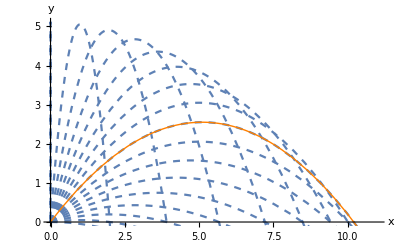

```mathematica
rules[θ_?NumericQ,vMag_?NumericQ]:=Evaluate[ParametricNDSolve[{x''[t]==0,y''[t]==-g, x[0]==0,y[0]==0,x'[0]==vMag*Cos[θ],y'[0]==vMag*Sin[θ]},{x,y},{t,0,maxT},{θ,vMag}]]
fncs[t_,θ_]:={Evaluate[x[θ,10][t]/.rules[θ, 10][[1]]],Evaluate[y[θ,10][t]/.rules[θ, 10][[2]]]}
p1 = ParametricPlot[Table[fncs[t,θ],{θ,0,Pi/2,Pi/32}],{t,0,3},PlotRange->{{0, 11},{0,Automatic}},AspectRatio->1/GoldenRatio,PlotStyle->Dashed,AxesLabel->{"x","y"}];
p2 = ParametricPlot[fncs[t,Pi/4],{t,0,3},PlotRange->{{0, 11},{0,Automatic}},AspectRatio->1/GoldenRatio,PlotStyle->{Orange,Thick},AxesLabel->{"x","y"}];
Show[p1,p2]
```

## Part 3

```mathematica
Clear[x,y]
grapefruitRules[θ_?NumericQ,vMag_?NumericQ]:=Evaluate[ParametricNDSolve[{x''[t]==-0.5*1.3*0.05^2*Sqrt[x'[t]^2+y'[t]^2]*x'[t]/0.5,y''[t]==-g-0.5*1.3*0.05^2*Sqrt[x'[t]^2+y'[t]^2]*y'[t]/0.5,x[0]==0,y[0]==0,x'[0]==vMag*Cos[θ],y'[0]==vMag*Sin[θ]},{x,y},{t,0,maxT},{θ,vMag}]]
trajectory[t_,θ_,vMag_]:={Evaluate[x[θ,vMag][t]/.grapefruitRules[θ, vMag][[1]]],Evaluate[y[θ,vMag][t]/.grapefruitRules[θ,vMag][[2]]]}
trajectory[t/.FindRoot[trajectory[t,optimalTheta,v0][[2]]==0,{t,maxT,0.1,maxT}], optimalTheta,v0][[1]]
```

333.33

## Part 4

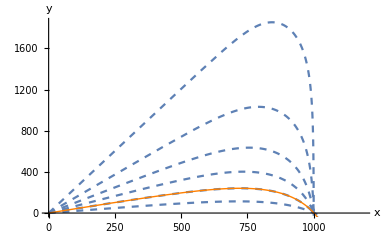

```mathematica
trajectories={trajectory[t,Pi/16,930],trajectory[t,Pi/8,770],trajectory[t,3*Pi/16,860],trajectory[t,2*Pi/8,1320],trajectory[t,5*Pi/16,3610],trajectory[t,3*Pi/8,40000]};
p1 = ParametricPlot[trajectories,{t,0,100},PlotRange->{{0, Automatic},{0,Automatic}},AspectRatio->1/GoldenRatio,PlotStyle->Dashed,AxesLabel->{"x","y"}];
p2 = ParametricPlot[trajectory[t,Pi/8,770],{t,0,100},PlotRange->{{0, Automatic},{0,Automatic}},AspectRatio->1/GoldenRatio,PlotStyle->{Orange,Thick},AxesLabel->{"x","y"}];
Show[p1,p2]
```

## Part 5

```mathematica
landingTime[θ_,v_]:=FindRoot[trajectory[t,θ,v][[2]]==0,{t,maxT,0.1,maxT}]
range[θ_,v_]:=trajectory[t/.landingTime[θ,v], θ,v][[1]]

(* Implement a binary search *)
findVelocity[{vMin_,vMax_}, θ_,target_]:=Module[
{max=vMax,min=vMin,v=vMin+(vMax-vMin)/2,eps=0.0001},
While[Abs[range[θ,v]-target]>eps,If[range[θ,v]-target>0,
max=v;v=min+(v-min)/2,
min=v;v=v+(max-v)/2];
];Return[v]]

(* Implement a gradient descent *)
velDeriv[θ_,target_]:=(findVelocity[{0,2000},θ+0.0001,target] - findVelocity[{0,2000},θ-0.0001,target])/0.0002
findAngle[target_]:=Module[
{currθ=Pi/4,
prevθ=Pi/6,
gamma = 0.0001,
eps= 0.000001,
prevStepSize = Pi/4},
While[prevStepSize > eps,
prevθ=currθ;
currθ += -gamma*velDeriv[currθ,target];
If[currθ<0,currθ=0.01];
If[currθ>Pi/2,currθ=Pi/2-0.01];
prevStepSize = Abs[currθ - prevθ];
];
Return[currθ]
]

(* Get the best angle in radians *)
angle = findAngle[1000]
(* Get the corresponding velocity to go 1000 m at that angle *)
N[findVelocity[{0,10000},angle,1000]]
```

0.410604

767.808